# Taylor Polynomials in Two and Three Dimensions

Joshua Pedro

## Taylor series in one dimension

Taylor series are a technique to approximate any infinitely differentiable function into a polynomial

Let’s consider the function.

```mathematica
f[x_]:=ⅇ^x
```

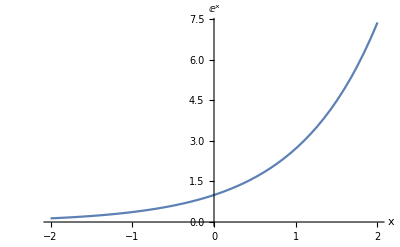

```mathematica
Plot[f[x],{x,-2,2},AxesLabel->{x,f[x]}]
```

Our goal is to approximate the function around 0. Lets first try with a linear function. The slope of a function is given by its derivative, so we can use that for our approximation

```mathematica
b=D[f[x],x]/.x->0
```

1

```mathematica
c=f[0]
```

1

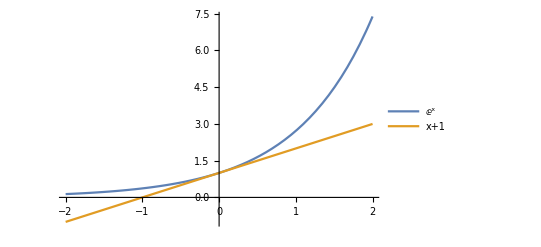

```mathematica
Plot[{f[x],b x+c},{x,-2,2},PlotLegends->{ⅇ^x,b x+c}]
```

This looks good near x = 0, but can we do better? Let’s consider a quadratic function. We use the same approach as above but this time we match the second derivatives at x=0 . The second derivative of f is

```mathematica
D[f[x],{x,2}]/.x->0
```

1

The second derivative of a x^2+b x+c at x=0 is

```mathematica
Clear[a,b]
```

```mathematica
D[a x^2 + b x+c,{x,2}]
```

2 a

Since we would like the second derivatives to match, we see that

```mathematica
a=1/2;
```

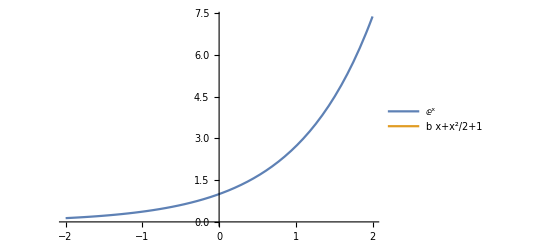

```mathematica
Plot[{f[x],a x^2+b x+c},{x,-2,2},PlotLegends->{ⅇ^x,a x^2+b x+c}]
```

We can repeat this process to generate higher order polynomials which approximate the function with greater accuracy. If we do this up to infinity, we get the Taylor series representation of our function around zero.

```mathematica
ⅇ^x===∑_(n=0)^∞ x^n/(n!)
```

True

Putting this together, we build an interactive model to show that the power series converges to the function with the more added terms.

```mathematica
Manipulate[Plot[{f[x],Evaluate[Normal[Series[f[x],{x,0,n}]]]},{x,-5,5},PlotRange->{{-3,3},{-2,8}},PlotLegends->Placed["Expressions",Bottom],AxesLabel->{x,f[x]}],{n,0,9,1},SaveDefinitions->True]
```

## Taylor series in two dimensions

Suppose now that our function is

```mathematica
f[x_,y_]:=ⅇ^(-x/2)Cos[2y]
```

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotRange->All,AxesLabel->Automatic,Boxed->False,AxesStyle->Thick,PlotPoints->60,PlotStyle->Directive[FaceForm[Yellow,Orange],Specularity[White,60],Opacity[0.8]],Axes->False]
```

-Graphics3D-

We would like to find our Taylor series approximation using our previous approach for univariate functions. However, higher order derivatives require tensor product calculations but Mathematica does this effortlessly.

First we define our Taylor series

```mathematica
multTaylorSeries[f_,x_,n_]:=∑_(i=0)^n 1/(i!)(D[f,{x,i}]/.Thread[x->0]).Sequence@@Table[x-0,i]
```

Now we create a plot showing the original surface along with our Taylor series approximation. Notice that as n gets larger, the Taylor polynomial wraps around the surface, near zero.

```mathematica
Manipulate[Plot3D[{f[x,y],Evaluate[multTaylorSeries[f[x,y],{x,y},n]]},{x,-5,5},{y,-5,5},AxesLabel->Automatic,PlotRange->{-15,15},Boxed->False,PlotStyle->{Directive[FaceForm[Yellow,Orange],Specularity[White,60],Opacity[0.6]],{Default,Opacity[0.85]}},ClippingStyle->None,Axes->False,PlotLegends->{f[x,y],"Taylor Polynomial"},PlotPoints->60],{n,0,30,1},SaveDefinitions->True]
```

Let’s look at what happens in the case of the three dimensional Gaussian bell curve.

```mathematica
g[x_,y_]:=ⅇ^(-(x^2+y^2))
```

```mathematica
multTaylorSeries2[f_,x_,n_]:=∑_(i=0)^n 1/(i!)(D[f,{x,i}]/.Thread[x->0]).Sequence@@Table[x-0,i]
```

```mathematica
Manipulate[Plot3D[{g[x,y],Evaluate[multTaylorSeries2[g[x,y],{x,y},n]]},{x,-5,5},{y,-5,5},AxesLabel->Automatic,PlotRange->{0,1},Boxed->False,PlotStyle->{Directive[GrayLevel[0],Specularity[White,60],Opacity[0.09]],{Default,Opacity[0.85]}},ClippingStyle->None,Axes->False,PlotLegends->{g[x,y],"Taylor Polynomial"},PlotPoints->60],{n,0,30,1},SaveDefinitions->True]
```